### Load FeynRules and model

```mathematica
Quit[]
```

```mathematica
$FeynRulesPath=NotebookDirectory[]<>"/feynrules-current";
<<FeynRules`
SetDirectory[$FeynRulesPath<>"/Models/Toponium"];
LoadModel["SM_Updated.fr","Toponium.fr"]
LoadRestriction["Cabibbo.rst",(*"Massless.rst",*)"DiagonalCKM.rst"]
```

- FeynRules -

Version: 2.3.49 ( 29 September 2021).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

Merging model-files...

This model implementation was created by

Jing-Hang Fu

Model Version: 1.0

Please cite

https://github.com/fujinghang/Toponium

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model Toponium loaded.

Global`a$::shdw: 符号 a$ 出现在多个上下文 {Global`,FeynRules`} 中；上下文 Global` 中的定义可能遮蔽或者被其他定义遮蔽.

Loading restrictions from Cabibbo.rst :  / 6

Loading restrictions from DiagonalCKM.rst :  / 3

Restrictions loaded.

```mathematica
CheckHermiticity[LSM+L1Et+L1Jt]
```

Checking for hermiticity by calculating the Feynman rules contained in L-HC[L].

If the lagrangian is hermitian, then the number of vertices should be zero.

Starting Feynman rule calculation.

Expanding the Lagrangian...

Expanding the indices over 16 cores

Collecting the different structures that enter the vertex.

No vertices found.

0 vertices obtained.

The lagrangian is hermitian.

{}

```mathematica
ComputeWidths[FeynmanRules[L1Et],Save->False];
%[[Position[%[[All,1,1]],Et]//Flatten]];
{%[[All,1]],
(%[[All,2]]*1000//NumericalValue)}//Transpose;
{%[[All,1]],(({%[[All,2]][[1]]*MZ^4/((MEt)^2-MH^2)^2}~Join~%[[All,2]][[2;;-1]])//NumericalValue)*MeV}//MatrixForm//NumberForm[#,{10,3}]&
GammattbWbW=(2*(1.3148+0.027*(MT-172.69))*(1-vv^2/8)//.vv->(gEt^2*64*Pi)^(1/3)//NumericalValue)*GeV;
%%[[2]]/1000/MeV*GeV//Total//NumberForm[#,{10,6}]&
{GammattbWbW,%+GammattbWbW}//NumberForm[#,{10,6}]&
{%%%%[[1]],%%%%[[2]]/1000/%[[2]]*10^4/MeV*GeV}//MatrixForm//NumberForm[#,{10,2}]&
{%%%/%%[[2]],%%[[1]]/%%[[2]]}*10^4//NumberForm[#,{10,2}]&
```

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

8 possible non-zero vertices have been found -> starting the computation:  / 8.

8 vertices obtained.

Flavor expansion of the vertices:  / 8

Computing the squared matrix elements relevant for the 1->2 decays:

/ 6

({Et,H,Z} | {Et,G,G} | {Et,W^†,W} | {Et,Z,Z} | {Et,A,A} | {Et,A,Z}
5.625 MeV | 15.864 MeV | 1.302 MeV | 0.067 MeV | 0.092 MeV | 0.023 MeV)

0.022971 GeV

{2.591813 GeV,2.614784 GeV}

({Et,H,Z} | {Et,G,G} | {Et,W^†,W} | {Et,Z,Z} | {Et,A,A} | {Et,A,Z}
21.51 | 60.67 | 4.98 | 0.25 | 0.35 | 0.09)

{87.85,9912.15}

```mathematica
ComputeWidths[FeynmanRules[L1Jt],Save->False];
%[[Position[%[[All,1,1]],Jt]//Flatten]];
{%[[All,1]],(%[[All,2]]*1000//NumericalValue)*MeV}//Transpose//MatrixForm//NumberForm[#,{10,3}]&
GammattbWbW=(2*(1.3148+0.027*(MT-172.69))*(1-vv^2/8)//.vv->(gJt^2*64*Pi)^(1/3)//NumericalValue)*GeV;
%%[[All,2]]/1000/MeV*GeV//Total//NumberForm[#,{10,6}]&
{GammattbWbW,%+GammattbWbW}//NumberForm[#,{10,6}]&
{%%%%[[All,1]],%%%%[[All,2]]/1000/%[[2]]*10^4/MeV*GeV}//Transpose//MatrixForm//NumberForm[#,{10,2}]&
{%%%/%%[[2]],%%[[1]]/%%[[2]]}*10^4//NumberForm[#,{10,2}]&
```

Starting Feynman rule calculation.

Expanding the Lagrangian...

Expanding the indices over 16 cores

Collecting the different structures that enter the vertex.

16 possible non-zero vertices have been found -> starting the computation:  / 16.

16 vertices obtained.

Flavor expansion of the vertices:  / 16

Computing the squared matrix elements relevant for the 1->2 decays:

/ 16

({Jt,A,H} | 0.609 MeV
{Jt,H,Z} | 0.081 MeV
{Jt,b,b^-} | 4.914 MeV
{Jt,c,c^-} | 0.134 MeV
{Jt,d,d^-} | 0.064 MeV
{Jt,e,e^-} | 0.078 MeV
{Jt,mu,mu^-} | 0.078 MeV
{Jt,s,s^-} | 0.064 MeV
{Jt,ta,ta^-} | 0.078 MeV
{Jt,u,u^-} | 0.134 MeV
{Jt,ve,ve^-} | 0.008 MeV
{Jt,vm,vm^-} | 0.008 MeV
{Jt,vt,vt^-} | 0.008 MeV
{Jt,W^†,W} | 5.466 MeV
{Jt,A,Z} | 0.703 MeV
{Jt,Z,Z} | 0.055 MeV)

0.012482 GeV

{2.591813 GeV,2.604295 GeV}

({Jt,A,H} | 2.34
{Jt,H,Z} | 0.31
{Jt,b,b^-} | 18.87
{Jt,c,c^-} | 0.52
{Jt,d,d^-} | 0.25
{Jt,e,e^-} | 0.30
{Jt,mu,mu^-} | 0.30
{Jt,s,s^-} | 0.25
{Jt,ta,ta^-} | 0.30
{Jt,u,u^-} | 0.52
{Jt,ve,ve^-} | 0.03
{Jt,vm,vm^-} | 0.03
{Jt,vt,vt^-} | 0.03
{Jt,W^†,W} | 20.99
{Jt,A,Z} | 2.70
{Jt,Z,Z} | 0.21)

{47.93,9952.07}

### generate FeynArts LO model

```mathematica
Quit
```

```mathematica
$FeynRulesPath=NotebookDirectory[]<>"/feynrules-current";
<<FeynRules`
SetDirectory[$FeynRulesPath<>"/Models/Toponium"];
LoadModel["SM_Updated.fr","Toponium.fr"]
LoadRestriction["Cabibbo.rst",(*"Massless.rst",*)"DiagonalCKM.rst"]
```

- FeynRules -

Version: 2.3.49 ( 29 September 2021).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

Merging model-files...

This model implementation was created by

Jing-Hang Fu

Model Version: 1.0

Please cite

https://github.com/fujinghang/Toponium

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model Toponium loaded.

Global`a$::shdw: 符号 a$ 出现在多个上下文 {Global`,FeynRules`} 中；上下文 Global` 中的定义可能遮蔽或者被其他定义遮蔽.

Loading restrictions from Cabibbo.rst :  / 6

Loading restrictions from DiagonalCKM.rst :  / 3

Restrictions loaded.

```mathematica
FeynmanGauge = True;
WriteFeynArtsOutput[L1JtZA,LSM+L1Et+L1Jt-L1JtZA,
Output->NotebookDirectory[]<>"FeynArts-3.12/Models/Toponium_LO_FA",
FlavorExpand->True]
```

- - - FeynRules interface to FeynArts - - -

C. Degrande C. Duhr, 2013

Counterterms: B. Fuks, 2012

Creating output directory: D:\work\toponium_FeynRules\Toponium_FeynRules\FeynArts-3.12/Models/Toponium_LO_FA

CreateDirectory::eexist: D:\work\toponium_FeynRules\Toponium_FeynRules\FeynArts-3.12\Models\Toponium_LO_FA 已经存在.

Calculating Feynman rules for L1

Calculating Feynman rules for L2

Redefining classes in such a way that each particle is in a separate FeynArts class.

See NewFeynArtsClasses[] for more information on the new classes

Restarting Feynman rule calculation, setting FlavorExpand -> True.

Calculating Feynman rules for L1

Starting Feynman rules calculation for L1.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

1 possible non-zero vertices have been found -> starting the computation:  / 1.

1 vertex obtained.

Calculating Feynman rules for L2

Starting Feynman rules calculation for L2.

Expanding the Lagrangian...

Expanding the indices over 16 cores

Collecting the different structures that enter the vertex.

177 possible non-zero vertices have been found -> starting the computation:  / 177.

162 vertices obtained.

mytimecheck,after LGC

Writing FeynArts model file into directory D:\work\toponium_FeynRules\Toponium_FeynRules\FeynArts-3.12/Models/Toponium_LO_FA

Writing FeynArts generic file on D:\work\toponium_FeynRules\Toponium_FeynRules\FeynArts-3.12/Models/Toponium_LO_FA.gen.

### generate LO UFO

```mathematica
Quit[]
```

```mathematica
$FeynRulesPath=NotebookDirectory[]<>"/feynrules-current";
<<FeynRules`
SetDirectory[$FeynRulesPath<>"/Models/Toponium"];
LoadModel["SM_Updated.fr","Toponium.fr"]
LoadRestriction["Cabibbo.rst",(*"Massless.rst",*)"DiagonalCKM.rst"]
```

- FeynRules -

Version: 2.3.49 ( 29 September 2021).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

Merging model-files...

This model implementation was created by

Jing-Hang Fu

Model Version: 1.0

Please cite

https://github.com/fujinghang/Toponium

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model Toponium loaded.

Global`a$::shdw: 符号 a$ 出现在多个上下文 {Global`,FeynRules`} 中；上下文 Global` 中的定义可能遮蔽或者被其他定义遮蔽.

Loading restrictions from Cabibbo.rst :  / 6

Loading restrictions from DiagonalCKM.rst :  / 3

Restrictions loaded.

```mathematica
WriteUFO[LSM+L1Et+L1Jt,Output->"Toponium_LO_UFO"]
```

--- Universal FeynRules Output (UFO) v 1.1 ---

Starting Feynman rule calculation.

Expanding the Lagrangian...

Expanding the indices over 16 cores

Collecting the different structures that enter the vertex.

60 possible non-zero vertices have been found -> starting the computation:  / 60.

55 vertices obtained.

Flavor expansion of the vertices distributed over 16 cores:  / 54

- Saved vertices in InterfaceRun[ 1 ].

Computing the squared matrix elements relevant for the 1->2 decays:

/ 58

Squared matrix elent compute in 3.14063 seconds.

/ 68

Decay widths computed in 0.65625 seconds.

Preparing Python output.

- Splitting vertices into building blocks.

Splitting of vertices distributed over 15 kernels.

- Optimizing: /86 .

- Writing files.

Done!

### FeynArts and Feynman Diagram

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"/FeynArts-3.12"];
<< FeynArts`
$FAVerbose=0;
```

FeynArts 3.12 (24 May 2024)

(patched for use with FeynCalc) by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

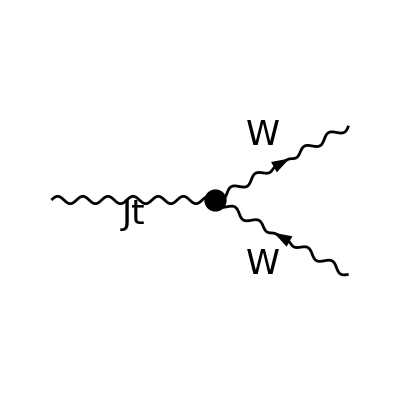

```mathematica
InsertFields[CreateTopologies[0,1->2],
(*{V[5]}->{F[12],-F[12]},*)
{V[5]}->{V[3],-V[3]},
Model->"Toponium_LO_FA",
GenericModel->"Toponium_LO_FA",
InsertionLevel->{Particles}];
Paint[%,Numbering->None,SheetHeader->None,ColumnsXRows->{1,1},ImageSize->{300,300}];
```

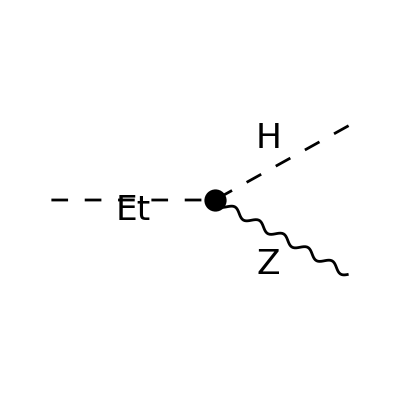

```mathematica
InsertFields[CreateTopologies[0,1->2],
(*{S[4]}->{V[4],V[4]},*)
(*{S[4]}->{V[3],-V[3]},*)
{S[4]}->{S[1],V[2]},
Model->"Toponium_LO_FA",
GenericModel->"Toponium_LO_FA",
InsertionLevel->{Particles}];
Paint[%,Numbering->None,SheetHeader->None,ColumnsXRows->{1,1},ImageSize->{300,300}];
```

## Test

### generate FeynArts QCD-NLO model

```mathematica
Quit[]
```

```mathematica
$FeynRulesPath=NotebookDirectory[]<>"/feynrules-current";
<<FeynRules`
SetDirectory[$FeynRulesPath<>"/Models/Toponium"];
LoadModel["SM_Updated.fr","Toponium.fr"]
LoadRestriction["Cabibbo.rst",(*"Massless.rst",*)"DiagonalCKM.rst"]
```

- FeynRules -

Version: 2.3.49 ( 29 September 2021).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

Merging model-files...

This model implementation was created by

Jing-Hang Fu

Model Version: 1.0

Please cite

https://github.com/fujinghang/Toponium

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model Toponium loaded.

Global`a$::shdw: 符号 a$ 出现在多个上下文 {Global`,FeynRules`} 中；上下文 Global` 中的定义可能遮蔽或者被其他定义遮蔽.

Loading restrictions from Cabibbo.rst :  / 6

Loading restrictions from DiagonalCKM.rst :  / 3

Restrictions loaded.

```mathematica
FeynmanGauge=True;
Lren=OnShellRenormalization[
LSM+L1Et+L1Jt,
QCDOnly->True];
WriteFeynArtsOutput[Lren,
Output->NotebookDirectory[]<>
"FeynArts-3.12/Models/Toponium_QCDNLO_FA",
FlavorExpand->True]
```

Extracting the mass and kinetic terms to simplify them

Neglecting all terms with more than 2 particles.

renormalizing the fields

All mixing allowed for the renormalization

renormalizing the parameters

Solve::nongen: 可能存在使某些解或所有解都无效的参数值.

renormalizing the masses

renormalizing the other external parameters

Internal parameter renormalization

renormalizing the Lagrangian

with the parameters

paramters before tadpole

with the fields

- - - FeynRules interface to FeynArts - - -

C. Degrande C. Duhr, 2013

Counterterms: B. Fuks, 2012

Creating output directory: D:\work\toponium_FeynRules\Toponium_FeynRules\FeynArts-3.12/Models/Toponium_QCDNLO_FA

CreateDirectory::eexist: D:\work\toponium_FeynRules\Toponium_FeynRules\FeynArts-3.12\Models\Toponium_QCDNLO_FA 已经存在.

Calculating Feynman rules for L1

Redefining classes in such a way that each particle is in a separate FeynArts class.

See NewFeynArtsClasses[] for more information on the new classes

Restarting Feynman rule calculation, setting FlavorExpand -> True.

Calculating Feynman rules for L1

Starting Feynman rules calculation for L1.

Expanding the Lagrangian...

Expanding the indices over 16 cores

Collecting the different structures that enter the vertex.

326 possible non-zero vertices have been found -> starting the computation:  / 326.

299 vertices obtained.

mytimecheck,after LGC

Writing FeynArts model file into directory D:\work\toponium_FeynRules\Toponium_FeynRules\FeynArts-3.12/Models/Toponium_QCDNLO_FA

Writing FeynArts generic file on D:\work\toponium_FeynRules\Toponium_FeynRules\FeynArts-3.12/Models/Toponium_QCDNLO_FA.gen.

### NLOCT: Computation of the Counter-terms

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"/FeynArts-3.12"];
<< FeynArts`
SetDirectory[NotebookDirectory[]<>"/feynrules-current"];
<< NLOCT`
```

FeynArts 3.12 (24 May 2024)

(patched for use with FeynCalc) by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

- NLOCT -

Version: 1.02

Authors: C. Degrande

Please cite C. Degrande, Comput.Phys.Commun. 197 (2015) 239-262

```mathematica
WriteCT//Options
```

{LabelInternal→True,KeptIndices→{},QCDOnly→False,ZeroMom→{},Assumptions→{},MSbar→False,ComplexMass→False,CTparameters→False,Exclude4ScalarsCT→False,Output→Automatic}

```mathematica
SetDirectory[NotebookDirectory[]<>"/feynrules-current/Models/Toponium"];
WriteCT["Toponium_QCDNLO_FA","Toponium_QCDNLO_FA",
Output->"Toponium_QCDNLO_CT",
QCDOnly->True]
```

Computing CT for the {S} vertices.

loading generic model file D:\work\toponium_FeynRules\Toponium_FeynRules\FeynArts-3.12\Models\Toponium_QCDNLO_FA.gen

> $GenericMixing is OFF

generic model {Toponium_QCDNLO_FA} initialized

loading classes model file D:\work\toponium_FeynRules\Toponium_FeynRules\FeynArts-3.12\Models\Toponium_QCDNLO_FA.mod

> 45 particles (incl. antiparticles) in 26 classes

> $CounterTerms are ON

> 139 vertices

> 148 counterterms of order 1

classes model {Toponium_QCDNLO_FA} initialized

inserting at level(s) {Generic,Classes}

> Top. 1: 4 Generic, 28 Classes insertions

in total: 4 Generic, 28 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

Writing amplitude finished after 0.1166724

Writing the R2 and UV parts at the class level finished after 0.1166724

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

in total: 0 Generic, 0 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

Writing the symbolic CT finished after 0.1166724

SU3 algebra finished after 0.1166724

Simplification of the vertices finished after 0.1166724

Vertices {S} finished after 0.1181810

Computing CT for the {F, F} vertices.

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

> Top. 2: 2 Generic, 138 Classes insertions

in total: 2 Generic, 138 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 12 Classes amplitudes

in total: 1 Generic, 12 Classes amplitudes

Writing amplitude finished after 0.2962590

Writing the R2 and UV parts at the class level finished after 0.2962590

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 36 Classes insertions

in total: 1 Generic, 36 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 36 Classes amplitudes

in total: 1 Generic, 36 Classes amplitudes

Part::partw: {} 的部分 1 不存在.

Writing the symbolic CT finished after 0.3685436

SU3 algebra finished after 0.3685436

Simplification of the vertices finished after 0.3685436

Vertices {F, F} finished after 0.3685436

Computing CT for the {S, S} vertices.

inserting at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 22 Classes insertions

> Top. 2: 5 Generic, 91 Classes insertions

in total: 7 Generic, 113 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

Writing amplitude finished after 0.4466251

Writing the R2 and UV parts at the class level finished after 0.4466251

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

in total: 0 Generic, 0 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

Writing the symbolic CT finished after 0.4501366

SU3 algebra finished after 0.4501366

Simplification of the vertices finished after 0.4501366

Vertices {S, S} finished after 0.4501366

Computing CT for the {V, V} vertices.

inserting at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 23 Classes insertions

> Top. 2: 5 Generic, 131 Classes insertions

in total: 7 Generic, 154 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes amplitudes

> Top. 2: 3 Generic, 32 Classes amplitudes

in total: 4 Generic, 33 Classes amplitudes

Writing amplitude finished after 0.6012997

Part::partw: {} 的部分 1 不存在.

Writing the R2 and UV parts at the class level finished after 1.0253268

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes insertions

in total: 1 Generic, 1 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes amplitudes

in total: 1 Generic, 1 Classes amplitudes

Writing the symbolic CT finished after 1.1410837

Part::partw: {} 的部分 1 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

SU3 algebra finished after 3.8280122

Simplification of the vertices finished after 5.8061071

Vertices {V, V} finished after 5.8061071

Computing CT for the {F, F, S} vertices.

inserting at level(s) {Generic,Classes}

> Top. 1: 6 Generic, 900 Classes insertions

> Top. 2: 0 Generic, 0 Classes insertions

> Top. 3: 0 Generic, 0 Classes insertions

> Top. 4: 0 Generic, 0 Classes insertions

in total: 6 Generic, 900 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 36 Classes amplitudes

in total: 1 Generic, 36 Classes amplitudes

Writing amplitude finished after 9.0487881

Writing the R2 and UV parts at the class level finished after 9.0497899

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 108 Classes insertions

in total: 1 Generic, 108 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 108 Classes amplitudes

in total: 1 Generic, 108 Classes amplitudes

Writing the symbolic CT finished after 9.1840210

SU3 algebra finished after 9.7233072

Simplification of the vertices finished after 15.1973671

Vertices {F, F, S} finished after 15.1973671

Computing CT for the {F, F, V} vertices.

inserting at level(s) {Generic,Classes}

> Top. 1: 6 Generic, 966 Classes insertions

> Top. 2: 0 Generic, 0 Classes insertions

> Top. 3: 0 Generic, 0 Classes insertions

> Top. 4: 0 Generic, 0 Classes insertions

in total: 6 Generic, 966 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 3 Generic, 132 Classes amplitudes

in total: 3 Generic, 132 Classes amplitudes

Writing amplitude finished after 19.1779558

Warning : More that 4 propagators, this diagram is discarded

Writing the R2 and UV parts at the class level finished after 19.2054890

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 144 Classes insertions

in total: 1 Generic, 144 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 144 Classes amplitudes

in total: 1 Generic, 144 Classes amplitudes

Writing the symbolic CT finished after 19.4193806

SU3 algebra finished after 50.3622160

Simplification of the vertices finished after 92.1941458

Vertices {F, F, V} finished after 92.1941458

Computing CT for the {V, V, V} vertices.

inserting at level(s) {Generic,Classes}

> Top. 1: 10 Generic, 943 Classes insertions

> Top. 2: 2 Generic, 57 Classes insertions

> Top. 3: 2 Generic, 57 Classes insertions

> Top. 4: 2 Generic, 57 Classes insertions

in total: 16 Generic, 1114 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 3 Generic, 267 Classes amplitudes

> Top. 2: 1 Generic, 1 Classes amplitudes

> Top. 3: 1 Generic, 1 Classes amplitudes

> Top. 4: 1 Generic, 1 Classes amplitudes

in total: 6 Generic, 270 Classes amplitudes

Writing amplitude finished after 93.5958815

Warning : More that 4 propagators, this diagram is discarded

Writing the R2 and UV parts at the class level finished after 93.6220090

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes insertions

in total: 1 Generic, 1 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes amplitudes

in total: 1 Generic, 1 Classes amplitudes

Writing the symbolic CT finished after 93.6789707

SU3 algebra finished after 411.9366832

Simplification of the vertices finished after 839.9440533

Vertices {V, V, V} finished after 839.9440533

Computing CT for the {V, V, S} vertices.

inserting at level(s) {Generic,Classes}

> Top. 1: 10 Generic, 778 Classes insertions

> Top. 2: 1 Generic, 45 Classes insertions

> Top. 3: 1 Generic, 45 Classes insertions

> Top. 4: 2 Generic, 44 Classes insertions

in total: 14 Generic, 912 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 144 Classes amplitudes

in total: 1 Generic, 144 Classes amplitudes

Writing amplitude finished after 840.9512879

Writing the R2 and UV parts at the class level finished after 840.9522879

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

in total: 0 Generic, 0 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

Writing the symbolic CT finished after 840.9543186

SU3 algebra finished after 840.9543186

Simplification of the vertices finished after 840.9543186

Vertices {V, V, S} finished after 840.9543186

Computing CT for the {V, S, S} vertices.

inserting at level(s) {Generic,Classes}

> Top. 1: 10 Generic, 666 Classes insertions

> Top. 2: 2 Generic, 42 Classes insertions

> Top. 3: 1 Generic, 54 Classes insertions

> Top. 4: 1 Generic, 54 Classes insertions

in total: 14 Generic, 816 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 60 Classes amplitudes

in total: 1 Generic, 60 Classes amplitudes

Writing amplitude finished after 841.7690570

Writing the R2 and UV parts at the class level finished after 841.7690570

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

in total: 0 Generic, 0 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

Writing the symbolic CT finished after 841.7710561

SU3 algebra finished after 841.7710561

Simplification of the vertices finished after 841.7710561

Vertices {V, S, S} finished after 841.7710561

Computing CT for the {S, S, S} vertices.

inserting at level(s) {Generic,Classes}

> Top. 1: 10 Generic, 593 Classes insertions

> Top. 2: 2 Generic, 42 Classes insertions

> Top. 3: 2 Generic, 42 Classes insertions

> Top. 4: 2 Generic, 42 Classes insertions

in total: 16 Generic, 719 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

Writing amplitude finished after 842.4552757

Writing the R2 and UV parts at the class level finished after 842.4552757

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

in total: 0 Generic, 0 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

in total: 0 Generic, 0 Classes amplitudes

Writing the symbolic CT finished after 842.4572755

SU3 algebra finished after 842.4572755

Simplification of the vertices finished after 842.4572755

Vertices {S, S, S} finished after 842.4572755

Computing CT for the {V, V, V, V} vertices.

Excluding 11 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 343 Classes insertions

> Top. 2: 2 Generic, 343 Classes insertions

> Top. 3: 2 Generic, 343 Classes insertions

> Top. 4: 2 Generic, 343 Classes insertions

> Top. 5: 2 Generic, 343 Classes insertions

> Top. 6: 2 Generic, 343 Classes insertions

> Top. 7: 4 Generic, 2479 Classes insertions

> Top. 8: 4 Generic, 2479 Classes insertions

> Top. 9: 4 Generic, 2479 Classes insertions

> Top. 10: 2 Generic, 233 Classes insertions

> Top. 11: 2 Generic, 233 Classes insertions

> Top. 12: 2 Generic, 233 Classes insertions

Restoring 11 field point(s)

in total: 30 Generic, 10194 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes amplitudes

> Top. 2: 1 Generic, 1 Classes amplitudes

> Top. 3: 1 Generic, 1 Classes amplitudes

> Top. 4: 1 Generic, 1 Classes amplitudes

> Top. 5: 1 Generic, 1 Classes amplitudes

> Top. 6: 1 Generic, 1 Classes amplitudes

> Top. 7: 3 Generic, 1143 Classes amplitudes

> Top. 8: 3 Generic, 1143 Classes amplitudes

> Top. 9: 3 Generic, 1143 Classes amplitudes

> Top. 10: 1 Generic, 1 Classes amplitudes

> Top. 11: 1 Generic, 1 Classes amplitudes

> Top. 12: 1 Generic, 1 Classes amplitudes

in total: 18 Generic, 3438 Classes amplitudes

Writing amplitude finished after 863.0222033

Warning : More that 4 propagators, this diagram is discarded

Warning : More that 4 propagators, this diagram is discarded

Warning : More that 4 propagators, this diagram is discarded

«6 more identical outputs»

Writing the R2 and UV parts at the class level finished after 877.8159927

inserting at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes insertions

in total: 1 Generic, 1 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes amplitudes

in total: 1 Generic, 1 Classes amplitudes

Writing the symbolic CT finished after 878.0409712

$Aborted

```mathematica
10213.88/60/60 hours
```

2.83719 hours

### generate QCD-NLO UFO

```mathematica
Quit[]
```

```mathematica
$FeynRulesPath=NotebookDirectory[]<>"/feynrules-current";
<<FeynRules`
SetDirectory[$FeynRulesPath<>"/Models/Toponium"];
LoadModel["SM_Updated.fr","Toponium.fr"]
LoadRestriction["Cabibbo.rst",(*"Massless.rst",*)"DiagonalCKM.rst"]
```

- FeynRules -

Version: 2.3.49 ( 29 September 2021).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

Merging model-files...

This model implementation was created by

Top 6

Model Version: 1.0

Please cite

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model Toponium loaded.

Global`a$::shdw: 符号 a$ 出现在多个上下文 {Global`,FeynRules`} 中；上下文 Global` 中的定义可能遮蔽或者被其他定义遮蔽.

Loading restrictions from Cabibbo.rst :  / 6

Loading restrictions from DiagonalCKM.rst :  / 3

Restrictions loaded.

```mathematica
Get[$FeynRulesPath<>"/Models/Toponium/Toponium_QCDNLO_CT.nlo"]
WriteUFO[LSM+L1Et+L1Jt,
UVCounterterms->UV$vertlist//.
Eps[FourVector[-xx__],
FourVector[FourMomentum[Internal,1]],Index[Lorentz,2],Index[Lorentz,4]]:>-Eps[FourVector[xx],FourVector[FourMomentum[Internal,1]],Index[Lorentz,2],Index[Lorentz,4]],
R2Vertices->R2$vertlist//.
Eps[FourVector[-xx__],
FourVector[FourMomentum[Internal,1]],Index[Lorentz,2],Index[Lorentz,4]]:>-Eps[FourVector[xx],FourVector[FourMomentum[Internal,1]],Index[Lorentz,2],Index[Lorentz,4]],
Output->"Toponium_QCDNLO_UFO"]
```

--- Universal FeynRules Output (UFO) v 1.1 ---

Starting Feynman rule calculation.

Expanding the Lagrangian...

Expanding the indices over 16 cores

Collecting the different structures that enter the vertex.

60 possible non-zero vertices have been found -> starting the computation:  / 60.

55 vertices obtained.

Flavor expansion of the vertices distributed over 16 cores:  / 117

- Saved vertices in InterfaceRun[ 1 ].

Computing the squared matrix elements relevant for the 1->2 decays:

/ 59

Squared matrix elent compute in 3.4375 seconds.

/ 68

Decay widths computed in 0.65625 seconds.

Preparing Python output.

- Splitting vertices into building blocks.

Splitting of vertices distributed over 15 kernels.

- Optimizing: /119 .

- Writing files.

Done!